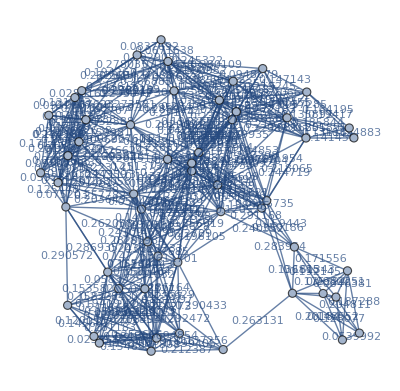

```mathematica
RandomWeightedGraphTriangleInequality[54,.3]
```

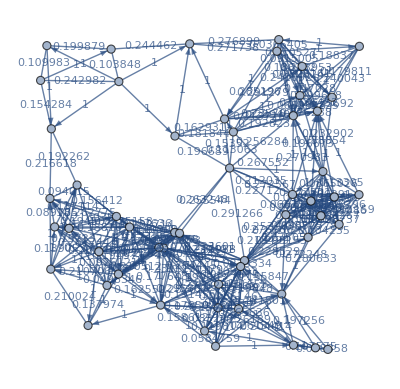

```mathematica
MixedGraph[RandomWeightedGraphTriangleInequality[54,.3],.4]
```

```mathematica
MakeUndirectedEdgesDirected[g_?GraphQ]:=Module[{undirectedEdges},undirectedEdges=Select[EdgeList[g],Head[#]==UndirectedEdge&];]
```

```mathematica
MakeUndirectedEdgesDirected[g_?ConnectedGraphQ]:=Module[{firstToLast,lastToFirst},firstToLast=Graph[Fold[EdgeAdd[#1,DirectedEdge[First[#2],Last[#2]]]&,g,Cases[EdgeList[g],_UndirectedEdge]],EdgeWeight->Join[Values[AssociationMap[AnnotationValue[{g,#},EdgeWeight]&,Cases[EdgeList[g],_UndirectedEdge]]],AnnotationValue[{g,#},EdgeWeight]&/@EdgeList[g]]];lastToFirst=Graph[Fold[EdgeAdd[#1,DirectedEdge[Last[#2],First[#2]]]&,firstToLast,Cases[EdgeList[firstToLast],_UndirectedEdge]],EdgeWeight->Join[Values[AssociationMap[AnnotationValue[{firstToLast,#},EdgeWeight]&,Cases[EdgeList[firstToLast],_UndirectedEdge]]],AnnotationValue[{firstToLast,#},EdgeWeight]&/@EdgeList[firstToLast]]]]
```

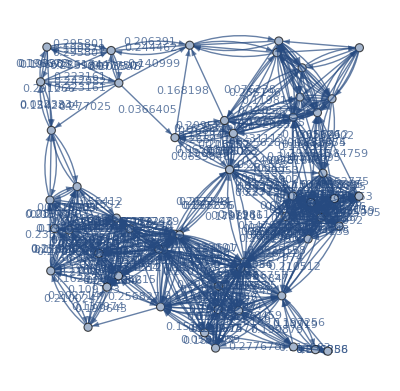

```mathematica
MakeUndirectedEdgesDirected[%15]
```

```mathematica
FindCycle[MakeUndirectedEdgesDirected[%15],Infinity,All]
```

FindCycle::ngen: The generalized FindCycle[Graph[<54>, <622>], Infinity, All] is not implemented.

FindCycle[-Graphics-,∞,All]

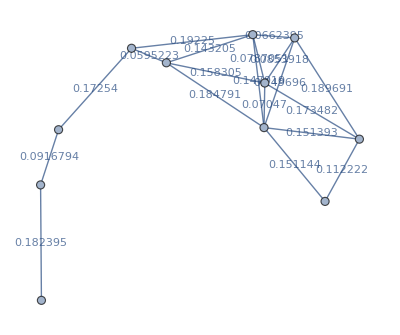

```mathematica
RandomWeightedGraphTriangleInequality[20,.2]
```

```mathematica
G=%23;
```

```mathematica
∑_(i=1)^VertexList[G] ∑_(j=1)^i Boole[MemberQ[EdgeList[G],UndirectedEdge[i,j]]]
```

0

```mathematica
VertexList[G]
```

{3,19,4,9,5,12,17,10,15,18,13}

```mathematica
Sum[AnnotationValue[{G,UndirectedEdge[i,j]},EdgeWeight]Boole[MemberQ[EdgeList[G],UndirectedEdge[i,j]]],{i,VertexList[G]},{j,VertexList[G]}]
```

2.56104

```mathematica
EdgeList[G]
```

{3<->19,3<->4,4<->19,3<->9,4<->9,3<->5,4<->5,5<->19,5<->9,3<->12,9<->12,4<->17,5<->17,17<->19,5<->10,10<->17,12<->15,15<->18,13<->18}

```mathematica
Boole@OddQ[Count[VertexList[G],v_/;OddQ[VertexDegree[G,v]]]]
```

0

```mathematica
Sum[Boole[OddQ[Count[s,v_/;OddQ[VertexDegree[G,v]]]]],{s,Subsets[VertexList[G]]}]
```

1024

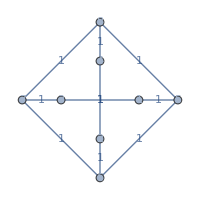

```mathematica
g=PetersenGraph[4,2,Sequence[VertexSize->Medium,VertexLabels->Placed["Name",Center],EdgeLabels->"EdgeWeight",ImageSize->200]]
```

```mathematica
L=(DiagonalMatrix[Total[#,{1}]]-#)&[WeightedAdjacencyMatrix[g]];
objective=-Total[Inactive[Times][L,Y],2];
```

```mathematica
n = Length[L];
decisionConstraints = {Table[Indexed[Y, {i, i}] == 1, {i, n}], 
   s == (Y + 1)/2, 0 \[VectorLessEqual] s \[VectorLessEqual] 1, Y 
(\[VectorGreaterEqual])_ 0};
```

```mathematica
res=SemidefiniteOptimization[objective,decisionConstraints,{Y∈Matrices[{n,n},Integers],s∈Matrices[{n,n},Integers]}]
```

{Y→{{1,-1,1,-1,-1,1,-1,1},{-1,1,-1,1,1,-1,1,-1},{1,-1,1,-1,-1,1,-1,1},{-1,1,-1,1,1,-1,1,-1},{-1,1,-1,1,1,-1,1,-1},{1,-1,1,-1,-1,1,-1,1},{-1,1,-1,1,1,-1,1,-1},{1,-1,1,-1,-1,1,-1,1}},s→{{1,0,1,0,0,1,0,1},{0,1,0,1,1,0,1,0},{1,0,1,0,0,1,0,1},{0,1,0,1,1,0,1,0},{0,1,0,1,1,0,1,0},{1,0,1,0,0,1,0,1},{0,1,0,1,1,0,1,0},{1,0,1,0,0,1,0,1}}}

```mathematica
subset=First[DeleteDuplicates[Y/. res]]
```

{1,-1,1,-1,-1,1,-1,1}

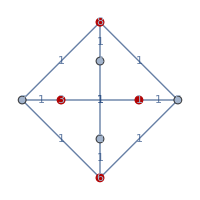

```mathematica
HighlightGraph[g,Pick[Range[n],subset,1]]
```

The objective is to maximize ∑_(i,j=1)^n w_(i j)(1-x_i x_j)=Tr ( L ·Y), where Y=x·Transpose[x] is a symmetric rank-1 positive semidefinite matrix and L is the Laplacian matrix of the graph:

The max-cut problem determines a subset S of the vertices V of a graph, for which the sum of the weights w_(i j) of the edges that cross from S to its complement V \ S is maximized. Let x_k=1 for k∈S and x_k=-1 for k∈V \ S. Maximize (1/4∑)_(i,j=1)^n w_(i j)(1-x_i x_j)=Tr (1/4 L · (x·xᵀ)), where x_k∈{-1, 1}, k=1,…, n and L is the Laplacian matrix of the graph:

```mathematica
L=(DiagonalMatrix[Total[#,{1}]]-#)&[WeightedAdjacencyMatrix[g]];
objective=-Total[Inactive[Times][L,Y],2];
```

```mathematica
n = Length[L];
decisionConstraints = {Table[Indexed[Y, {i, i}] == 1, {i, n}], 
   s == (Y + 1)/2, 0 \[VectorLessEqual] s \[VectorLessEqual] 1, Y 
(\[VectorGreaterEqual])_ 0};
```

```mathematica
res=SemidefiniteOptimization[objective,decisionConstraints,{Y∈Matrices[{n,n},Integers],s∈Matrices[{n,n},Integers]}]
```

{Y→{{1,-1,1,-1,-1,1,-1,1},{-1,1,-1,1,1,-1,1,-1},{1,-1,1,-1,-1,1,-1,1},{-1,1,-1,1,1,-1,1,-1},{-1,1,-1,1,1,-1,1,-1},{1,-1,1,-1,-1,1,-1,1},{-1,1,-1,1,1,-1,1,-1},{1,-1,1,-1,-1,1,-1,1}},s→{{1,0,1,0,0,1,0,1},{0,1,0,1,1,0,1,0},{1,0,1,0,0,1,0,1},{0,1,0,1,1,0,1,0},{0,1,0,1,1,0,1,0},{1,0,1,0,0,1,0,1},{0,1,0,1,1,0,1,0},{1,0,1,0,0,1,0,1}}}

```mathematica
L=(DiagonalMatrix[Total[#,{1}]]-#)&[WeightedAdjacencyMatrix[g]];
objective=Total[Inactive[Times][L,Y],2];
```

```mathematica
n = Length[L];
decisionConstraints = {Table[Indexed[Y, {i, i}] == 1, {i, n}], 
   s == (Y + 1)/2, 0 \[VectorLessEqual] s \[VectorLessEqual] 1, Y 
(\[VectorGreaterEqual])_ 0};
```

```mathematica
res=SemidefiniteOptimization[objective,decisionConstraints,{Y∈Matrices[{n,n},Integers],s∈Matrices[{n,n},Integers]}]
```

{Y→{{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}},s→{{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}}}